```mathematica
Quiet@Remove["Global`*"];
n = 10;
data = Table[N[{x, Sin[x]}], {x, 0., 2Pi, 2Pi/n}];
```

```mathematica
lpl = ListPlot[data, PlotStyle->{Red, PointSize[0.015]}];
i0 = 3;
int = Interpolation[data, InterpolationOrder->i0];
{xmin, xmax}= int[[1,1]];
Show[lpl, Plot[int[x], {x, xmin, xmax}], Plot[Sin[x], {x, xmin,xmax}, PlotStyle->{Black, Dashed}]];
Plot[{int''[x], Sin''[x]}, {x, xmin,xmax}];
```

```mathematica
Quiet@Remove["Global`*"];
n = 100;
data = Flatten[Table[N[{x,y, Sin[x+2y]}], {x, 0, 2Pi, 2Pi/n}, {y, 0, 2Pi, 2Pi/n}], 1];
int = Interpolation[data];
{{xmin,xmax}, {ymin,ymax}} = int[[1]];
Plot3D[Sin[x+2y]- int[x,y], {x, xmin, xmax}, {y, ymin, ymax}]
```

-Graphics3D-

{0==-2. (5.99039-1. a-1. b-c)-1.28 (5.17813-0.64 a-0.8 b-c)-0.72 (4.55236-0.36 a-0.6 b-c)-0.32 (3.95932-0.16 a-0.4 b-c)-0.08 (3.39341-0.04 a-0.2 b-c)-0.08 (2.58826-0.04 a+0.2 b-c)-0.32 (2.42926-0.16 a+0.4 b-c)-0.72 (2.22873-0.36 a+0.6 b-c)-1.28 (2.01952-0.64 a+0.8 b-c)-2. (2.05792-1. a+1. b-c)-2.88 (1.94134-1.44 a+1.2 b-c)-3.92 (2.10736-1.96 a+1.4 b-c)-5.12 (2.30737-2.56 a+1.6 b-c)-6.48 (2.68022-3.24 a+1.8 b-c)-8. (2.95031-4. a+2. b-c),0==-2. (5.99039-1. a-1. b-c)-1.6 (5.17813-0.64 a-0.8 b-c)-1.2 (4.55236-0.36 a-0.6 b-c)-0.8 (3.95932-0.16 a-0.4 b-c)-0.4 (3.39341-0.04 a-0.2 b-c)+0.4 (2.58826-0.04 a+0.2 b-c)+0.8 (2.42926-0.16 a+0.4 b-c)+1.2 (2.22873-0.36 a+0.6 b-c)+1.6 (2.01952-0.64 a+0.8 b-c)+2. (2.05792-1. a+1. b-c)+2.4 (1.94134-1.44 a+1.2 b-c)+2.8 (2.10736-1.96 a+1.4 b-c)+3.2 (2.30737-2.56 a+1.6 b-c)+3.6 (2.68022-3.24 a+1.8 b-c)+4. (2.95031-4. a+2. b-c),0==-2 (2.91495-c)-2 (5.99039-1. a-1. b-c)-2 (5.17813-0.64 a-0.8 b-c)-2 (4.55236-0.36 a-0.6 b-c)-2 (3.95932-0.16 a-0.4 b-c)-2 (3.39341-0.04 a-0.2 b-c)-2 (2.58826-0.04 a+0.2 b-c)-2 (2.42926-0.16 a+0.4 b-c)-2 (2.22873-0.36 a+0.6 b-c)-2 (2.01952-0.64 a+0.8 b-c)-2 (2.05792-1. a+1. b-c)-2 (1.94134-1.44 a+1.2 b-c)-2 (2.10736-1.96 a+1.4 b-c)-2 (2.30737-2.56 a+1.6 b-c)-2 (2.68022-3.24 a+1.8 b-c)-2 (2.95031-4. a+2. b-c)}

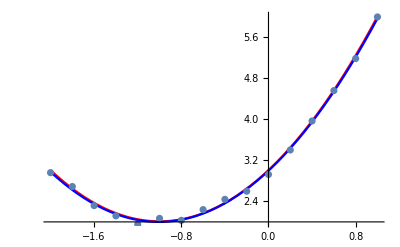

{2.98785+1.98609 x+0.987611 x^2,2.98785+1.98609 x+0.987611 x^2}

```mathematica
Quiet@Remove["Global`*"];
rn := 0.1*RandomReal[{-1,1}];
f[x_] := x^2+ 2x + 3;
data = Table[{x, f[x]+ rn}, {x, -2, 1, 0.2}];
ListPlot[data];
err[{x_,y_}]:= (y- (a*x^2+ b*x + c))^2
totalError =Total[err/@data];
eqnsForCriticalPoints = 0 == D[totalError, #]&/@{a,b,c}
ruleforABC = Solve[eqnsForCriticalPoints][[1]];
y = a*x^2+b*x + c/.ruleforABC;
Show[Plot[{f[x], y}, {x, -2, 1}, PlotStyle->{Red, Blue}], ListPlot[data]]
{Fit[data, {1, x, x^2}, x], y}
```

```mathematica
Quiet@Remove["Global`*"];
f[t_]:= 5 + 10*Exp[-4t];
data = Table[N[{t, f[t]}], {t, 0, 1, 1/10}];
ListPlot[data];
FindFit[data, a+b*Exp[-c*t], {a,b,c}, t]
```

{a→5.,b→10.,c→4.}